```mathematica
Clear[phystest];
Clear[zero];
Clear[Σ];
Clear[Subscript[a, 1]];
Clear[Subscript[a, 2]];
Clear[Subscript[a, 3]];
Clear[SuperPlus[Subscript[e, 12]]];
Clear[SuperMinus[Subscript[e, 12]]];
Clear[SuperPlus[Subscript[e, 23]]];
Clear[SuperMinus[Subscript[e, 23]]];
Clear[SuperPlus[Subscript[e, 13]]];
Clear[SuperMinus[Subscript[e, 13]]];
Clear[cp];
Clear[cm];
Clear[covm];
```

```mathematica
Subscript[a, 1]=Table[RandomReal[{1,10}],{i,10^4}];
Subscript[a, 2]=Table[RandomReal[{1,10}],{i,10^4}];
Subscript[a, 3]=Table[RandomReal[{1,10}],{i,10^4}];
```

```mathematica
a1=Table[Subscript[a, 1][[i]]-1,{i,10^4}];
a2=Table[Subscript[a, 2][[i]]-1,{i,10^4}];
a3=Table[Subscript[a, 3][[i]]-1,{i,10^4}];

(*these values a1,a2,a3 are all greater than 0*)

Subscript[a, 1][[1]]
a1[[1]]
a1;
```

1.68787

0.687867

```mathematica
Do[If[Abs[a1[[i]]-a2[[i]]]<a3[[i]]<a1[[i]]+a2[[i]]&&Abs[a1[[i]]-a3[[i]]]<a2[[i]]<a1[[i]]+a3[[i]]
&&Abs[a2[[i]]-a3[[i]]]<a1[[i]]<a2[[i]]+a3[[i]]
,Print[{i ,a1[[i]],a2[[i]],a3[[i]]}],Print["NO"]]
,{i,10^4}];

(*Only currently evaluating the first inequality, need to refine the values of aj[[i]] more to include the second 2 inequalities also.*)
Dynamic[i]
```

NO

NO

{3,5.92291,5.69511,4.03756}

NO

{5,5.82728,7.14474,5.00704}

{6,6.47716,2.91407,8.65048}

{7,6.33396,8.90203,3.02392}

{8,7.0958,7.62916,6.63787}

NO

NO

{11,8.18741,8.43514,5.42832}

NO

NO

NO

{15,4.89924,3.75205,8.06032}

{16,4.28175,5.88886,5.97548}

NO

{18,6.87709,6.73926,7.14475}

{19,7.56569,7.48164,3.8941}

NO

NO

{22,4.2868,5.7414,7.45095}

{23,7.49152,8.41768,5.69036}

{24,4.34522,3.65969,1.10841}

{25,5.5083,7.94254,8.62938}

{26,7.89416,3.66239,4.57991}

{27,6.6338,7.7202,1.66665}

{28,3.09291,8.14614,5.87884}

NO

{30,6.64559,6.50528,3.05871}

NO

{32,5.50641,4.93605,7.4265}

NO

{34,3.83967,2.87917,4.84966}

{35,8.44576,4.94455,8.24067}

{36,7.86771,5.8346,7.8548}

{37,2.00127,5.969,5.07501}

{38,4.67084,3.96784,8.1893}

{39,8.98968,7.39368,7.02283}

{40,4.46501,0.779612,4.7694}

NO

{42,3.02104,4.41557,6.74398}

NO

{44,8.03824,5.81645,7.4346}

{45,1.13552,1.35717,1.57457}

{46,1.98864,3.99026,4.07549}

NO

{48,1.91696,2.3596,2.11071}

{49,2.91379,3.81271,2.13824}

NO

{51,5.81776,5.88695,6.44865}

NO

{53,7.63854,1.46151,8.01432}

{54,6.73451,8.44356,4.24757}

{55,8.64184,8.15257,1.23042}

NO

{57,1.72363,2.32299,0.734479}

{58,2.95849,5.26331,3.50042}

{59,8.38004,7.59203,8.51907}

{60,5.94125,6.59433,1.71061}

{61,5.52847,4.44108,8.9245}

NO

{63,5.38648,5.06827,7.05352}

NO

NO

NO

{67,6.61789,7.16234,8.56264}

{68,7.91285,1.04841,7.03037}

{69,8.42228,6.02018,6.94985}

NO

{71,8.83155,4.49479,4.39932}

{72,7.86478,7.99956,8.44329}

NO

{74,5.59623,8.91427,5.74337}

{75,3.41407,0.890992,2.73633}

NO

{77,8.40842,6.68014,5.89633}

{78,3.61712,3.2392,4.87865}

NO

{80,4.85608,4.74401,1.99531}

NO

NO

{83,6.92444,7.49043,2.0948}

{84,5.87905,8.38989,3.55457}

{85,6.8921,2.92511,4.83729}

{86,8.13049,6.0803,7.14558}

{87,5.06362,5.14136,2.49546}

NO

NO

{90,7.45486,8.17139,1.06834}

NO

{92,7.28234,6.50712,4.56012}

{93,1.49545,4.09932,4.05293}

NO

NO

NO

«3 more identical outputs»

{100,7.45821,7.95893,1.64417}

{101,6.75209,7.11991,5.29276}

NO

{103,2.58376,3.69357,1.44282}

{104,7.02513,3.81868,6.52454}

NO

NO

{107,4.44454,4.98031,8.8084}

{108,7.70802,8.87745,3.45452}

NO

{110,2.66915,1.24513,1.69464}

{111,7.61226,2.49661,7.5164}

NO

NO

{114,8.39635,6.51636,7.2171}

{115,4.47944,1.50897,4.01439}

{116,3.1021,3.86552,2.58417}

NO

NO

NO

«3 more identical outputs»

{123,7.62227,7.35203,5.72486}

NO

{125,4.55344,5.55051,2.85467}

{126,3.22807,5.05058,4.71871}

{127,5.61243,5.43912,6.07705}

NO

{129,6.71747,8.49877,3.31897}

{130,4.24845,1.57055,4.88344}

NO

{132,8.39001,5.16581,4.1713}

{133,5.36833,6.35125,4.6206}

NO

NO

NO

«1 more identical outputs»

{138,2.69094,3.34325,2.41674}

NO

{140,0.508667,1.83597,1.38028}

{141,4.43982,4.27863,4.70347}

{142,6.03889,3.93998,6.27382}

{143,2.80297,6.01795,5.44031}

NO

NO

NO

«3 more identical outputs»

{150,7.82662,8.1497,5.30852}

{151,1.95352,1.55726,1.51466}

{152,7.73224,5.17723,7.9052}

{153,6.79206,8.83742,3.45296}

{154,2.39599,7.0397,6.58076}

NO

NO

NO

{158,4.8121,5.84533,8.0075}

NO

NO

NO

«2 more identical outputs»

{164,7.86268,8.16642,1.85279}

NO

NO

NO

{168,3.08978,2.82739,5.89479}

{169,8.05185,4.84872,7.65807}

{170,6.36682,3.41652,6.73032}

{171,1.11122,5.8544,5.9688}

{172,2.18758,3.88344,2.3288}

{173,7.9057,1.58823,8.99167}

NO

{175,2.78047,6.79855,8.55074}

NO

{177,4.60687,4.09157,8.57327}

NO

NO

{180,4.63172,5.93234,2.12913}

NO

{182,3.79057,3.38704,2.47838}

{183,5.44698,2.65669,3.60112}

{184,8.34096,7.21743,7.87955}

NO

{186,5.82713,2.21576,4.89186}

{187,4.71798,6.08688,2.86589}

{188,0.625355,4.13537,4.68887}

NO

{190,5.84032,5.43069,5.86362}

{191,4.36338,5.58612,3.44766}

NO

NO

{194,1.99042,1.22755,2.27339}

{195,2.58293,5.42958,3.35314}

NO

NO

{198,5.18264,6.43297,6.75979}

NO

NO

{201,8.67396,7.50751,5.70347}

NO

{203,4.88199,4.49327,5.36966}

{204,5.70608,8.42955,4.77292}

NO

NO

{207,6.80411,8.32834,4.04336}

NO

NO

NO

{211,3.86952,4.49361,2.55742}

NO

{213,5.96167,8.16369,8.06026}

{214,7.67638,1.8963,7.88808}

NO

NO

NO

«2 more identical outputs»

{220,4.88838,1.20158,3.75031}

NO

{222,8.84889,6.73909,4.94609}

NO

{224,4.91882,7.21578,2.66158}

NO

{226,6.34534,2.98055,4.32058}

{227,4.42768,2.52967,2.04899}

NO

NO

NO

«2 more identical outputs»

{233,3.06847,2.53299,0.565913}

{234,6.73987,6.55319,3.08637}

NO

NO

{237,7.41785,1.10527,7.85322}

{238,6.97802,4.2838,6.47005}

{239,2.68194,7.63715,5.34655}

{240,8.97178,6.36658,7.67249}

{241,2.54958,4.02772,3.5071}

NO

{243,8.67806,8.96026,8.28299}

{244,1.38447,6.35071,7.39043}

NO

NO

{247,6.20837,4.16252,7.71543}

NO

NO

{250,4.02312,2.81162,3.64114}

NO

{252,1.96105,2.04092,0.477797}

{253,7.93549,4.48846,8.50278}

NO

NO

NO

{257,5.55471,7.78933,5.61802}

{258,5.12037,2.73313,5.72689}

NO

NO

{261,3.33745,1.48198,3.00511}

{262,2.734,8.87762,7.15138}

{263,5.92046,6.28509,3.32177}

{264,4.42054,7.4936,8.03652}

NO

{266,5.10886,6.26702,7.49826}

{267,5.46967,6.70753,3.91582}

NO

NO

NO

«2 more identical outputs»

{273,6.41992,7.09498,8.02276}

{274,3.45401,5.00598,2.25415}

{275,0.400262,6.38393,6.10212}

{276,6.40057,7.86948,8.39007}

{277,2.36127,3.66986,4.847}

NO

{279,1.71509,4.96294,6.08284}

NO

NO

NO

{283,8.12768,5.65802,5.38885}

NO

NO

{286,7.41807,7.51667,3.6268}

{287,8.98497,8.3894,4.9325}

{288,6.83967,0.132641,6.85835}

{289,2.47342,1.36067,1.1901}

{290,2.13099,2.13126,2.38138}

{291,3.90265,4.40708,3.71048}

{292,1.96698,3.02784,2.37973}

NO

NO

{295,2.25601,1.43814,3.03043}

{296,1.28552,1.582,2.73064}

NO

NO

{299,3.31666,1.37683,3.12086}

NO

{301,3.21724,2.11194,2.2218}

NO

{303,7.48596,8.51316,5.86805}

NO

{305,2.47424,7.06258,5.03985}

NO

{307,6.64514,6.88054,0.554428}

{308,1.57421,8.01352,7.87945}

{309,5.38462,3.51854,4.62593}

NO

NO

NO

«1 more identical outputs»

{314,4.47291,6.66268,3.3773}

NO

NO

{317,0.961763,5.43698,4.98642}

NO

NO

{320,3.39499,1.72963,4.0491}

{321,8.23775,8.79418,4.56611}

NO

NO

{324,3.7185,3.31262,0.407772}

{325,6.12054,1.37585,7.18101}

NO

NO

NO

«1 more identical outputs»

{330,2.12653,6.92776,8.51991}

{331,4.82342,8.19443,3.91445}

NO

{333,8.7787,3.14744,8.24964}

{334,6.39487,0.764785,6.28373}

{335,4.68273,8.78262,8.87559}

{336,5.33188,7.00233,3.88841}

{337,8.86014,7.97297,7.1508}

{338,8.88622,4.91494,5.32716}

NO

NO

{341,7.19475,7.02429,4.08709}

NO

{343,8.07273,4.28885,5.28001}

{344,5.01563,4.47699,8.01417}

NO

NO

NO

«2 more identical outputs»

{350,7.77082,1.71582,7.81337}

NO

NO

NO

«2 more identical outputs»

{356,6.59405,4.50539,5.83127}

NO

{358,5.62265,3.95835,7.32114}

NO

NO

NO

«1 more identical outputs»

{363,4.59824,7.21495,4.72954}

{364,6.07624,7.37304,3.63372}

{365,2.67525,1.78577,0.897226}

NO

NO

{368,2.02528,7.57476,8.37293}

NO

NO

NO

«3 more identical outputs»

{375,4.63659,4.09212,5.6157}

{376,5.05387,6.78778,2.88108}

{377,2.28561,7.2164,8.82077}

NO

{379,5.29165,7.38904,7.40382}

NO

{381,7.48645,8.36921,2.56675}

{382,8.77934,4.50515,4.93264}

NO

NO

{385,2.27187,4.91412,2.70413}

NO

NO

NO

«1 more identical outputs»

{390,6.88556,3.97335,4.85562}

NO

NO

NO

{394,2.47894,7.23259,7.01777}

{395,2.28308,5.74155,6.75189}

{396,7.95839,1.80639,8.93655}

{397,1.86043,6.38697,5.73168}

{398,7.82623,5.62679,6.57344}

{399,5.92559,6.63424,0.998898}

NO

NO

NO

«1 more identical outputs»

{404,5.43977,5.32826,7.3491}

NO

NO

{407,6.0862,8.13868,7.26067}

NO

{409,4.06792,5.35926,3.44256}

NO

NO

NO

{413,6.74219,6.09071,5.12036}

{414,7.84687,6.75342,5.25782}

NO

{416,4.09036,8.33656,7.21287}

NO

{418,2.53534,4.30931,6.48359}

NO

{420,3.30616,0.546546,3.58868}

NO

NO

{423,7.0788,4.39231,3.72466}

{424,5.45791,8.38545,4.48795}

{425,6.79741,5.25499,2.50392}

NO

NO

{428,5.06421,4.83932,8.26219}

NO

{430,8.26494,6.10258,4.21544}

{431,5.13115,6.08388,7.56898}

NO

NO

NO

«3 more identical outputs»

{438,0.82809,1.45287,1.32274}

NO

NO

{441,7.05671,3.67548,7.6287}

{442,2.08272,6.84512,7.1885}

NO

NO

{445,3.26106,7.26256,7.08983}

NO

{447,1.8867,4.56184,4.36797}

NO

NO

{450,8.46085,5.17045,7.96768}

NO

{452,8.70363,6.63945,7.01401}

NO

NO

{455,5.54643,7.31342,2.22837}

{456,2.30873,2.25778,4.46722}

{457,5.33532,6.18146,7.83753}

{458,8.79551,2.77114,6.68276}

{459,4.71012,6.23444,6.53089}

NO

{461,4.56472,4.43844,0.661244}

NO

NO

NO

«2 more identical outputs»

{467,6.8385,7.38053,6.06228}

NO

NO

NO

«1 more identical outputs»

{472,6.64595,2.67585,8.34513}

{473,6.30852,5.08166,3.73757}

NO

NO

NO

«3 more identical outputs»

{480,7.00216,6.20758,8.04366}

{481,5.54283,4.68346,7.80977}

NO

{483,6.93266,7.2725,7.00774}

NO

{485,3.36355,1.31839,4.53838}

{486,5.17643,5.0811,1.38326}

NO

NO

{489,6.36964,7.41876,4.94722}

{490,3.1822,3.78111,3.20981}

{491,5.35994,4.25752,8.29758}

{492,7.09323,2.48025,4.81217}

{493,7.53321,4.75923,5.71594}

NO

{495,6.71939,7.73056,5.81424}

{496,4.04948,5.06203,3.56147}

{497,5.27255,7.08942,3.77922}

{498,2.50015,4.46915,4.34424}

{499,8.38579,2.7247,6.19278}

{500,6.26559,5.30261,4.62776}

{501,7.30938,4.86031,4.59669}

NO

NO

NO

«2 more identical outputs»

{507,1.90356,3.80484,5.31793}

NO

{509,3.6707,5.27798,4.64692}

{510,5.30089,7.41109,2.86001}

NO

{512,6.07047,7.15692,5.76772}

NO

NO

NO

«1 more identical outputs»

{517,5.13753,7.38277,6.2952}

{518,3.47871,2.98107,1.38574}

NO

{520,8.55965,4.3783,6.88834}

NO

NO

NO

{524,1.32851,1.84444,0.767447}

{525,6.93891,6.99093,8.33667}

{526,7.47276,4.01714,6.60665}

NO

{528,5.13891,5.80987,3.98613}

{529,5.36629,1.27831,5.03364}

NO

{531,5.42745,0.270527,5.15927}

{532,3.10954,8.15585,8.52751}

NO

{534,3.35154,2.8429,2.46529}

NO

{536,7.10864,3.70531,5.2242}

NO

NO

{539,6.28888,8.60909,2.71118}

{540,5.58357,4.12385,7.84876}

{541,6.64988,3.70074,8.92033}

{542,5.17161,7.01719,6.74507}

{543,7.19519,7.79264,6.93967}

NO

{545,8.64969,8.06154,8.10491}

{546,6.31479,8.03952,6.50596}

NO

{548,5.31129,6.69947,4.91601}

{549,6.6922,5.86067,5.41085}

NO

NO

NO

{553,3.82976,1.90935,4.99002}

NO

NO

NO

{557,3.74098,5.96621,6.54071}

{558,8.05117,3.59724,8.76269}

{559,4.58855,3.49307,5.92817}

NO

{561,4.69058,5.88737,8.60436}

{562,5.24383,5.25615,0.105065}

{563,3.41226,7.31499,8.61282}

{564,8.5476,4.17155,6.14453}

{565,1.81685,0.788452,1.56211}

NO

NO

NO

«1 more identical outputs»

{570,5.77118,2.66908,6.31197}

NO

{572,8.47445,6.00561,6.15392}

NO

NO

{575,2.73169,5.51571,4.43439}

{576,8.70512,4.34008,5.28703}

{577,6.9968,3.13915,5.84955}

NO

{579,6.7392,7.17419,7.46795}

{580,5.4746,3.60345,8.41171}

{581,7.50957,2.27037,7.81641}

{582,7.65278,6.03418,5.65005}

NO

NO

NO

{586,8.27264,2.65453,6.99327}

{587,3.59896,3.59869,5.25552}

NO

{589,3.63574,1.98547,3.79001}

{590,2.9478,5.9233,3.59959}

NO

{592,4.12965,3.56462,7.41007}

NO

NO

NO

«2 more identical outputs»

{598,5.51156,7.57057,6.84454}

NO

{600,5.76103,6.18804,0.695382}

{601,3.84149,8.41552,7.15266}

{602,5.8944,7.5814,4.18433}

{603,2.98273,2.5675,4.91778}

{604,7.03804,4.87551,8.54057}

NO

NO

{607,6.05863,6.20298,8.25625}

NO

NO

NO

«1 more identical outputs»

{612,6.41489,4.53411,8.13704}

NO

{614,7.09786,8.26186,8.65569}

NO

NO

NO

«1 more identical outputs»

{619,6.22186,8.1508,2.51225}

NO

{621,2.57323,3.31752,1.67141}

{622,3.71075,2.82743,2.18018}

{623,3.66717,5.65117,7.19178}

NO

NO

NO

«1 more identical outputs»

{628,2.35642,3.41918,2.05906}

NO

NO

NO

{632,2.63143,5.2019,5.84647}

{633,5.122,7.28826,6.87937}

NO

NO

NO

{637,5.80499,5.38042,7.13728}

{638,8.06375,3.02667,5.63235}

NO

NO

NO

{642,0.176805,2.4353,2.59181}

{643,8.0444,2.92844,8.35239}

{644,4.49684,3.6596,6.30956}

{645,6.5903,2.86221,5.59983}

NO

{647,2.03157,6.31367,7.86574}

{648,5.71816,5.3972,5.00776}

{649,8.78016,7.08804,3.55548}

NO

{651,5.48654,4.82078,3.12586}

{652,2.13532,1.62834,2.26153}

{653,5.80594,4.59205,4.38455}

NO

NO

NO

«1 more identical outputs»

{658,1.54693,6.3141,5.94538}

NO

{660,4.40535,5.34882,2.79263}

{661,3.76394,2.1015,2.44111}

{662,5.06555,5.48178,6.69368}

{663,4.54601,3.50438,7.08853}

NO

NO

{666,7.01966,4.64568,8.2978}

NO

{668,6.22122,8.927,4.76564}

{669,6.46375,6.08996,4.34198}

{670,7.0349,2.94237,8.59605}

NO

{672,7.97949,7.31779,3.40678}

NO

{674,8.5781,1.36005,7.74726}

{675,8.83361,6.46758,2.94482}

NO

{677,3.00684,6.44722,8.27406}

NO

NO

{680,7.65852,3.14654,6.68881}

NO

NO

NO

«2 more identical outputs»

{686,7.72811,8.00108,0.769854}

{687,6.44234,2.78363,3.76068}

{688,3.98328,5.07064,1.50441}

{689,5.88859,5.62981,3.59338}

NO

{691,8.48424,7.70921,3.28262}

NO

{693,5.87649,6.71109,1.02591}

NO

NO

{696,3.58454,2.86466,3.06522}

NO

NO

{699,4.13939,6.23461,2.50014}

{700,2.02391,4.46316,3.45568}

NO

{702,5.67548,4.60583,4.14743}

{703,6.33529,7.35318,5.86103}

{704,7.57078,3.02532,8.65593}

NO

NO

NO

«3 more identical outputs»

{711,5.25791,8.61817,4.19936}

NO

NO

NO

«2 more identical outputs»

{717,3.81097,6.37918,5.0489}

{718,2.8445,8.67898,8.14146}

NO

{720,5.45981,4.63605,8.92308}

NO

{722,6.45838,6.56407,4.20876}

{723,7.63906,6.42732,3.21088}

{724,6.53721,1.18792,5.78399}

NO

NO

NO

{728,3.86208,2.22789,4.92131}

NO

{730,5.05065,4.23588,5.46777}

{731,8.0125,7.2019,4.84096}

{732,0.432313,1.81774,1.77338}

{733,2.1505,1.7973,1.39396}

NO

NO

NO

«1 more identical outputs»

{738,6.84502,5.38128,7.92292}

{739,7.6169,6.03947,7.70215}

NO

{741,2.4284,7.76668,6.61464}

{742,3.50537,4.72324,2.08209}

NO

{744,5.38459,8.91634,6.61981}

NO

{746,2.17089,8.52327,8.93317}

{747,1.23074,7.77696,6.78266}

{748,6.70565,0.581953,7.22638}

{749,2.73432,1.51863,4.12204}

NO

NO

{752,4.77529,7.8543,4.21477}

{753,6.78592,8.59896,5.1558}

NO

{755,7.62689,5.66527,4.58008}

{756,5.7649,8.73887,5.92611}

{757,4.2858,3.94394,3.76987}

{758,6.22462,3.54824,4.07319}

NO

{760,6.73799,8.70838,6.69859}

NO

NO

{763,5.64693,6.30116,4.86777}

{764,1.86905,5.11405,3.84664}

NO

{766,5.57681,6.86819,2.17561}

{767,3.92557,7.49978,6.96482}

NO

NO

{770,1.46222,1.37161,0.164767}

NO

{772,4.97216,2.69558,4.71714}

{773,3.2422,5.57035,7.57406}

{774,6.0066,7.45369,3.28651}

{775,7.75645,6.19874,2.64801}

NO

{777,1.55899,2.52021,4.00063}

NO

{779,4.0766,8.20414,4.15862}

NO

{781,7.09264,6.65055,7.53838}

{782,1.96104,7.14837,8.68984}

{783,8.85244,4.11392,7.43311}

{784,3.62634,3.0469,2.04963}

{785,4.86634,7.12091,6.33852}

{786,4.65344,3.14366,6.54534}

NO

NO

NO

«4 more identical outputs»

{794,6.35848,7.84847,6.42479}

{795,3.7086,5.37848,8.53957}

NO

NO

{798,5.19326,4.68069,1.75576}

{799,2.60229,3.60816,3.66072}

NO

{801,7.72975,4.25569,7.75673}

NO

{803,5.44593,3.12411,6.92051}

NO

NO

NO

{807,0.74589,5.62981,5.78707}

NO

NO

{810,8.07241,3.95396,7.46626}

{811,8.6593,6.85879,4.20494}

{812,5.95564,4.87026,5.6169}

{813,4.66676,4.98536,7.59397}

{814,5.92814,8.53106,6.91774}

NO

{816,8.09773,4.56494,8.28136}

{817,3.14499,7.74623,6.04838}

NO

{819,5.76017,7.2059,2.63081}

{820,6.94109,6.12995,8.64255}

NO

NO

{823,8.79045,5.22187,4.26571}

{824,1.21777,3.79379,3.17142}

NO

{826,6.24833,1.43231,6.31926}

{827,6.1941,8.02206,2.13629}

{828,3.5859,3.52538,3.48433}

NO

NO

NO

{832,3.78749,7.2397,5.98518}

{833,6.73854,7.14932,7.338}

NO

{835,1.9893,4.40398,3.38716}

NO

NO

{838,7.54965,4.89814,3.28674}

{839,7.79143,1.70241,6.25858}

NO

{841,4.1861,5.94527,2.40114}

{842,5.76488,7.2879,4.82771}

NO

NO

NO

«4 more identical outputs»

{850,4.37322,5.87413,6.20357}

NO

NO

NO

«1 more identical outputs»

{855,7.75343,7.00329,5.11644}

{856,5.76532,3.16448,3.38474}

{857,3.84282,3.87964,0.379796}

NO

{859,8.08179,8.96995,1.53855}

NO

NO

{862,3.105,6.32246,7.10973}

NO

{864,5.47524,5.39615,6.17029}

{865,1.5042,6.93893,6.54937}

{866,1.33641,7.27648,8.35114}

{867,4.2804,3.86507,7.63126}

NO

{869,4.14051,6.32317,4.85319}

NO

NO

{872,6.18924,8.04041,2.39713}

{873,3.30129,1.63717,4.37612}

{874,8.23912,1.18125,7.73396}

NO

NO

{877,8.80779,8.52229,7.87441}

{878,7.71939,8.53489,3.93273}

{879,6.42884,5.25663,2.40084}

NO

NO

{882,6.01441,6.69584,3.69093}

NO

{884,6.13789,4.29113,8.49105}

NO

NO

NO

«1 more identical outputs»

{889,6.33119,7.4906,3.93152}

{890,8.33881,7.24114,2.05075}

{891,7.00611,7.23283,0.947421}

{892,5.86042,7.32095,8.17453}

NO

{894,6.73329,2.72492,4.29792}

NO

NO

NO

{898,8.80272,5.24947,8.23455}

NO

{900,5.77707,4.97469,4.03605}

{901,1.20282,5.13272,4.57417}

{902,7.31596,4.96894,7.24934}

{903,6.65992,8.71282,6.63817}

{904,7.08022,8.94122,2.7481}

{905,5.419,5.22877,1.40092}

NO

{907,3.66963,7.66911,5.89042}

NO

{909,6.81981,4.35407,4.40009}

NO

NO

{912,7.14114,4.36275,7.7938}

NO

NO

NO

«1 more identical outputs»

{917,7.44794,7.58411,4.73176}

NO

{919,6.56896,8.15044,5.6846}

NO

NO

NO

«1 more identical outputs»

{924,8.79759,3.48341,7.60741}

NO

{926,8.96419,5.80923,3.38196}

{927,6.02914,6.33322,7.59193}

{928,5.3191,6.52929,6.59056}

NO

{930,7.19817,4.94594,7.22394}

{931,7.03137,8.2822,8.44242}

NO

{933,7.69463,4.32151,6.40406}

{934,6.43485,3.30424,4.84525}

{935,3.82701,5.83098,7.38171}

NO

{937,4.73057,3.79112,6.09804}

NO

{939,5.82653,4.07316,7.91679}

NO

NO

NO

«2 more identical outputs»

{945,8.05743,4.60346,3.92398}

{946,7.02365,4.19688,8.93434}

{947,5.14532,3.56718,3.29829}

NO

{949,6.72957,6.82929,8.51385}

NO

NO

NO

«1 more identical outputs»

{954,6.27218,5.24643,5.95108}

NO

NO

NO

{958,8.56102,7.50745,2.44588}

{959,3.00567,5.58115,7.47961}

NO

{961,7.12287,5.31681,1.89363}

{962,4.52112,4.95033,2.72955}

NO

NO

{965,8.93203,4.62082,8.80021}

{966,4.04779,2.01998,4.6989}

NO

NO

{969,8.98031,8.24704,1.05279}

NO

NO

NO

{973,7.28634,4.62694,6.46115}

{974,1.47912,6.10444,6.98285}

{975,7.82079,8.49418,8.76965}

NO

NO

{978,8.94431,7.53578,4.56288}

{979,5.54795,3.52869,5.48308}

{980,4.34368,4.90208,3.0467}

NO

{982,7.51319,7.84473,0.380165}

{983,5.41125,6.75945,4.74973}

{984,6.17859,3.8652,7.80691}

NO

{986,6.92015,1.65856,5.77448}

NO

NO

NO

«1 more identical outputs»

{991,5.59061,2.25751,6.44044}

{992,5.93375,2.43627,5.95191}

NO

{994,2.21189,2.32341,2.36573}

NO

{996,6.54895,3.77241,8.92771}

{997,4.2888,3.10902,5.08133}

{998,3.19725,5.44281,5.98769}

{999,4.89676,6.86227,3.54303}

{1000,5.34849,6.05176,1.14008}

NO

NO

{1003,8.1692,7.84822,5.97285}

NO

NO

{1006,6.22831,5.60766,8.73857}

{1007,1.30024,4.45673,5.19312}

{1008,8.55679,7.07625,4.0598}

NO

NO

NO

«2 more identical outputs»

{1014,6.44107,3.90337,8.42507}

NO

NO

{1017,1.02509,2.21203,2.64952}

NO

NO

NO

{1021,4.12163,0.382805,4.37907}

NO

{1023,2.26181,8.59498,7.24589}

NO

{1025,6.2769,5.92732,2.9357}

{1026,3.83693,5.70415,6.75733}

NO

{1028,5.73793,2.96223,4.66969}

NO

{1030,4.30248,5.35849,1.90112}

{1031,8.31127,3.84885,6.62269}

{1032,3.41903,8.74013,5.39816}

{1033,4.39002,2.81808,5.22304}

NO

NO

NO

«2 more identical outputs»

{1039,6.68305,3.92053,4.47303}

{1040,6.95062,2.56214,8.3754}

NO

{1042,6.97803,8.17515,6.46918}

{1043,7.31111,4.66125,8.69564}

NO

NO

{1046,7.85877,4.76682,8.28284}

NO

{1048,3.2374,6.29186,8.45728}

{1049,7.98049,7.16949,5.54175}

NO

{1051,6.48778,6.55855,6.71447}

{1052,8.22043,6.97091,4.24026}

NO

NO

NO

«1 more identical outputs»

{1057,0.305895,5.63427,5.90661}

NO

{1059,6.57028,4.61698,7.46409}

{1060,7.07856,6.03004,7.29366}

NO

NO

{1063,3.92259,4.43752,4.27483}

{1064,0.0695779,7.17962,7.17048}

NO

NO

NO

«1 more identical outputs»

{1069,2.01383,5.16687,4.58731}

{1070,4.87409,3.48818,6.41255}

NO

{1072,4.13256,3.28614,6.01246}

{1073,1.20037,1.93309,1.79583}

NO

NO

NO

«2 more identical outputs»

{1079,6.42077,3.22372,7.65108}

NO

NO

NO

«1 more identical outputs»

{1084,6.95482,7.25347,6.73476}

{1085,2.64585,1.94748,2.19877}

{1086,4.52516,4.18145,2.81007}

NO

{1088,6.60522,3.12945,4.94455}

{1089,4.57664,8.97978,4.93652}

NO

NO

NO

{1093,8.0746,7.60622,0.518719}

{1094,0.858058,1.04663,0.724409}

{1095,1.77908,3.64887,5.04074}

NO

NO

{1098,7.07344,5.8295,4.64523}

{1099,4.89234,7.60484,8.15764}

{1100,7.79793,6.94565,8.08599}

NO

{1102,5.77676,1.97195,4.45234}

NO

NO

{1105,1.71497,3.93084,4.56204}

{1106,6.78194,7.19868,2.41033}

{1107,4.9763,7.38636,6.63625}

NO

NO

NO

«1 more identical outputs»

{1112,6.64431,3.61971,5.45214}

{1113,7.0235,8.14642,3.75136}

{1114,6.1453,7.72896,2.96094}

NO

NO

NO

«2 more identical outputs»

{1120,5.09173,7.65864,3.00405}

{1121,4.28202,4.84392,1.80954}

{1122,5.71075,7.17597,1.93323}

NO

NO

{1125,6.30881,7.79386,3.86764}

{1126,1.47085,6.08598,7.4372}

{1127,1.34649,2.97731,3.14156}

NO

NO

NO

{1131,4.3656,5.51032,5.85978}

NO

{1133,2.1597,1.64792,2.48523}

NO

NO

NO

{1137,8.96462,4.71023,6.54294}

NO

NO

NO

{1141,6.63342,8.71521,6.07421}

{1142,2.37372,5.61134,5.29534}

{1143,8.0333,3.40221,5.71902}

NO

NO

{1146,6.55992,4.55575,7.20474}

{1147,7.64902,6.40069,5.33593}

{1148,5.86495,7.5809,8.91958}

NO

{1150,2.27123,2.14357,2.40283}

NO

NO

{1153,5.38734,5.88433,0.714421}

NO

NO

{1156,4.23202,1.72034,3.09248}

{1157,3.45979,1.51602,3.05972}

{1158,7.45323,1.34762,6.87746}

NO

{1160,5.97224,3.58012,8.02973}

NO

{1162,4.9615,6.73476,8.78735}

{1163,5.54094,8.77673,6.9692}

{1164,6.48992,5.14573,4.27763}

{1165,7.37682,7.21252,5.49165}

{1166,5.54536,6.52312,7.07128}

{1167,1.44553,2.37939,2.2254}

{1168,5.98046,6.29797,2.50536}

{1169,6.34621,6.45038,2.21772}

{1170,5.3201,2.42169,6.85057}

{1171,4.65732,3.84653,7.28577}

{1172,2.01971,2.62025,2.74797}

NO

NO

{1175,6.36508,8.21426,6.15532}

NO

{1177,3.54966,7.98295,7.10515}

NO

NO

NO

«2 more identical outputs»

{1183,8.57456,6.85275,2.30513}

{1184,3.54409,1.85547,2.92202}

{1185,6.25081,3.40541,8.33192}

NO

NO

{1188,8.27624,4.03747,5.3462}

NO

NO

{1191,7.70196,3.33612,8.13368}

NO

{1193,3.76519,4.53177,4.32381}

NO

{1195,5.66328,2.74929,8.17904}

{1196,6.16428,2.51745,4.62623}

{1197,7.94747,7.64578,0.310255}

{1198,4.74131,7.88477,7.70879}

NO

{1200,4.68949,6.00422,2.15652}

NO

NO

{1203,8.67507,4.90282,6.19444}

{1204,7.3594,7.7877,3.52966}

{1205,7.89988,3.87132,5.0565}

{1206,5.62162,0.334232,5.94892}

NO

{1208,6.91034,8.90623,2.70016}

{1209,7.23999,1.78097,6.48645}

NO

{1211,4.10773,5.64584,6.90316}

NO

{1213,5.18127,4.10729,3.16232}

NO

NO

NO

«1 more identical outputs»

{1218,2.66098,7.89201,8.86052}

{1219,1.91979,4.1683,2.9709}

NO

{1221,6.14616,4.19147,3.39188}

NO

NO

{1224,3.53153,5.76927,5.20291}

NO

{1226,4.00139,4.7477,3.69253}

{1227,1.44132,1.99994,2.065}

{1228,6.8867,3.57247,3.63713}

{1229,8.44235,5.04171,4.84166}

{1230,8.82078,6.92276,3.43261}

NO

NO

NO

{1234,2.19991,3.56659,4.42929}

NO

NO

NO

«1 more identical outputs»

{1239,8.187,7.25493,1.95829}

{1240,7.35934,4.14642,4.02284}

{1241,6.98193,2.91648,7.70767}

NO

{1243,6.24734,5.50009,6.86255}

{1244,4.51357,6.60788,7.10839}

NO

{1246,4.70737,6.74043,8.44581}

{1247,4.48923,6.08133,7.53124}

NO

NO

NO

{1251,3.23095,1.43496,3.42773}

NO

{1253,1.44711,7.11915,5.90047}

{1254,7.35936,4.64722,5.01545}

{1255,5.40388,8.62385,3.81655}

NO

NO

{1258,7.7932,7.17499,5.72526}

{1259,6.2346,6.93173,4.30056}

{1260,6.73971,6.64133,8.73637}

NO

{1262,6.47559,8.03173,7.92353}

{1263,8.83419,2.4934,8.84737}

{1264,2.26129,2.26569,0.0987393}

NO

NO

{1267,6.01456,3.68336,2.6821}

NO

NO

{1270,7.36173,7.30266,2.51775}

{1271,6.57685,3.31318,4.26338}

{1272,7.74093,7.7694,1.83331}

{1273,7.6271,4.01537,8.85145}

{1274,6.9767,8.76763,1.94716}

NO

NO

NO

«4 more identical outputs»

{1282,6.56552,7.56074,4.30085}

{1283,7.43601,7.31205,7.22664}

NO

{1285,5.14247,7.32576,5.12673}

NO

NO

{1288,7.10916,8.87613,8.39035}

NO

NO

NO

{1292,3.36134,5.42963,8.7367}

{1293,5.58362,3.6167,4.33715}

NO

{1295,8.82736,3.73828,7.16139}

NO

NO

NO

{1299,4.08311,8.0824,7.72874}

NO

NO

NO

{1303,8.49951,8.13538,4.31737}

{1304,6.1038,3.03612,3.33535}

NO

{1306,2.4644,5.49996,3.37361}

NO

{1308,1.3347,6.51057,5.57546}

NO

{1310,7.00754,3.87085,3.2398}

{1311,3.29418,8.85001,6.43598}

{1312,2.75134,5.56579,3.63451}

{1313,4.97656,5.87643,2.2731}

{1314,3.35406,2.79944,2.50727}

NO

NO

NO

«3 more identical outputs»

{1321,6.9582,8.62826,5.82874}

{1322,4.42398,5.39279,6.37744}

NO

{1324,7.21296,1.01735,6.82881}

{1325,6.57584,5.69954,5.14349}

NO

NO

{1328,8.18439,6.4041,4.12209}

{1329,3.82577,5.38267,8.69641}

{1330,5.30932,5.21423,6.92636}

NO

NO

{1333,8.98424,7.66046,5.34311}

{1334,3.32746,2.9789,0.820266}

NO

NO

NO

«2 more identical outputs»

{1340,5.87192,6.16931,0.921224}

{1341,8.86673,7.22079,4.29677}

NO

NO

NO

{1345,2.95419,4.00261,5.57514}

{1346,3.39067,3.21315,1.44485}

{1347,2.03173,5.8004,5.94617}

{1348,3.65582,7.12379,8.17047}

NO

{1350,4.64484,7.06358,5.22185}

NO

{1352,7.67068,2.41361,8.34055}

{1353,5.59235,2.60543,3.00741}

{1354,5.53613,3.43106,6.63412}

NO

NO

NO

{1358,6.72322,0.868196,7.06512}

{1359,6.68389,3.38712,8.42782}

{1360,5.28141,2.47949,3.98802}

{1361,4.85607,3.90753,1.02056}

{1362,3.86606,5.12873,5.19183}

NO

NO

NO

{1366,1.79473,6.71451,6.38929}

NO

NO

{1369,8.69633,6.78798,5.49911}

NO

NO

NO

{1373,8.36159,6.26435,5.88829}

NO

{1375,3.52767,3.13715,1.35371}

{1376,3.96121,4.18645,1.94157}

NO

{1378,6.61298,4.02393,4.22067}

{1379,3.02367,3.17842,1.9885}

{1380,1.47732,0.573554,1.73258}

{1381,5.6914,5.01929,2.97393}

NO

{1383,5.16714,7.99955,3.86251}

NO

NO

NO

{1387,5.48578,2.37573,3.40818}

{1388,5.26692,7.50929,3.84406}

NO

NO

NO

«2 more identical outputs»

{1394,7.86368,7.81024,6.22882}

{1395,5.52968,8.26116,7.76115}

{1396,8.58839,7.54573,3.23705}

{1397,6.5665,8.74685,7.42668}

NO

NO

{1400,3.46889,6.20192,3.96609}

{1401,6.92481,6.32913,5.40033}

NO

{1403,7.62283,5.95625,7.38631}

NO

{1405,4.23289,3.31569,1.25185}

NO

{1407,1.60227,8.23637,8.05056}

NO

{1409,8.57115,8.14671,2.30319}

{1410,3.72651,5.33209,6.70342}

{1411,3.96725,4.87097,6.20616}

NO

{1413,5.91958,5.53375,7.02226}

NO

{1415,7.31078,2.60889,5.98631}

NO

NO

{1418,3.61272,1.05173,4.00944}

NO

{1420,3.23817,4.27183,4.65929}

{1421,4.8874,7.71187,3.83268}

{1422,4.10063,2.01091,3.04557}

{1423,6.13649,3.54644,6.19194}

NO

{1425,3.62504,0.636766,3.66461}

{1426,5.28237,4.43181,8.13949}

{1427,5.55133,1.32183,4.81458}

{1428,4.17124,2.23399,4.7142}

{1429,7.83794,5.73193,2.48304}

NO

NO

NO

{1433,3.37269,6.11853,3.63627}

NO

NO

{1436,6.35975,7.3188,2.72406}

{1437,5.52226,4.07689,3.71339}

NO

NO

NO

{1441,3.21937,4.78139,3.0821}

NO

NO

{1444,6.74178,8.54156,5.64311}

{1445,7.41227,6.61697,7.72613}

NO

{1447,3.40111,4.87528,1.77381}

NO

NO

NO

{1451,6.86848,3.92654,3.38843}

{1452,7.77678,8.43479,7.43238}

{1453,3.09202,1.28564,1.84311}

NO

NO

NO

{1457,3.75609,6.97309,8.18571}

NO

NO

NO

«1 more identical outputs»

{1462,3.21163,3.89509,6.68444}

NO

{1464,3.9063,6.88054,7.51917}

NO

{1466,2.08301,6.89676,8.17657}

{1467,8.16376,8.37216,0.831422}

NO

NO

{1470,1.62196,6.29645,5.42635}

NO

NO

NO

«2 more identical outputs»

{1476,3.73314,3.70184,2.69585}

NO

NO

NO

«9 more identical outputs»

{1489,7.25022,5.69389,1.79648}

{1490,1.56315,6.53751,6.04852}

{1491,5.59678,7.19254,5.37134}

{1492,4.50569,5.27261,6.72926}

{1493,7.24883,8.74146,1.90735}

{1494,5.75716,7.02388,8.10695}

NO

NO

NO

«1 more identical outputs»

{1499,5.91015,7.29863,5.77255}

{1500,7.87313,6.48953,5.45637}

{1501,3.06293,1.58129,3.97319}

NO

NO

{1504,5.67296,5.91504,0.330596}

{1505,8.73212,2.99791,6.7252}

NO

{1507,7.98809,5.93795,3.43736}

{1508,3.62769,2.2291,5.84641}

NO

{1510,8.32645,6.26008,8.33491}

NO

NO

NO

{1514,5.2313,1.39041,5.90457}

NO

NO

{1517,7.61398,4.42617,8.8293}

NO

NO

NO

{1521,5.27577,2.9132,7.82564}

{1522,6.7238,5.80682,7.97474}

{1523,4.85844,4.07049,3.91482}

NO

{1525,1.57073,2.02727,1.76274}

{1526,8.05666,8.30533,4.15899}

{1527,4.34457,3.30073,6.95253}

{1528,5.5418,5.00211,4.96925}

NO

NO

{1531,8.66528,6.37045,3.4835}

{1532,7.59771,7.07303,6.76351}

{1533,4.44841,6.49751,4.44049}

NO

NO

NO

{1537,4.60784,7.77168,7.96009}

{1538,5.38482,5.30525,5.33554}

NO

{1540,4.12046,5.86537,6.80846}

{1541,6.96875,5.00679,4.21511}

NO

NO

NO

{1545,7.72697,8.36543,6.99845}

NO

NO

{1548,2.93659,8.19639,5.97617}

{1549,6.21345,6.52635,7.26729}

{1550,1.60923,8.23641,8.77576}

NO

NO

NO

{1554,6.48739,7.86869,5.77561}

NO

{1556,8.53856,2.31947,6.60386}

{1557,1.87203,2.71067,1.34597}

NO

NO

{1560,7.07767,2.27748,7.53344}

{1561,6.4201,8.94995,8.03757}

{1562,5.75765,5.24557,4.95354}

NO

{1564,1.35245,6.50132,6.97973}

NO

{1566,8.4067,2.85031,6.82274}

NO

{1568,5.71913,6.30259,1.73205}

{1569,7.24675,3.38341,7.98237}

{1570,3.96093,7.4159,7.70467}

{1571,5.81952,4.15781,2.7217}

{1572,3.99035,3.34119,6.32812}

{1573,5.62493,8.64103,4.75866}

NO

NO

NO

«2 more identical outputs»

{1579,5.96775,6.74392,6.26515}

NO

NO

NO

{1583,1.9885,3.74987,3.34666}

NO

{1585,7.83181,8.5313,7.84476}

{1586,4.87763,4.40148,6.47719}

NO

NO

{1589,8.21551,5.5371,3.83701}

NO

{1591,3.44487,3.26458,3.83517}

{1592,8.68944,7.46754,5.36247}

NO

{1594,2.26753,6.37407,5.02917}

NO

NO

{1597,5.28301,6.64145,1.71822}

NO

{1599,2.64222,6.5014,8.13641}

NO

{1601,7.33674,3.4129,4.92745}

NO

NO

NO

«2 more identical outputs»

{1607,7.67269,2.79668,8.98246}

NO

{1609,4.44254,4.27966,1.86779}

{1610,1.28635,7.41538,6.37239}

{1611,4.2676,5.90444,7.09918}

{1612,8.02656,7.58835,2.52299}

{1613,5.27787,8.25215,5.55142}

NO

{1615,5.47913,2.43559,6.58212}

NO

NO

{1618,6.70821,8.96483,8.0213}

{1619,6.46739,8.16556,4.07228}

NO

{1621,6.89491,2.59811,7.93541}

{1622,3.31028,2.61411,3.2475}

{1623,6.63886,3.95565,3.5956}

{1624,6.25278,5.22835,1.22286}

{1625,1.94733,6.51528,6.12509}

{1626,2.43769,6.27142,8.30735}

NO

NO

{1629,2.38139,8.57926,8.79892}

{1630,4.42174,4.63169,3.7142}

NO

NO

{1633,2.75051,8.59955,8.96422}

NO

{1635,1.47217,7.99898,7.53135}

{1636,3.84339,8.50447,4.98746}

{1637,5.05014,5.58418,5.00149}

{1638,5.00105,8.30284,3.91468}

NO

NO

NO

{1642,1.10665,2.21855,1.64547}

{1643,6.50036,4.38329,6.74079}

{1644,7.50751,3.26034,7.77783}

{1645,6.04723,5.51661,1.51712}

NO

NO

NO

{1649,7.31984,1.83085,8.75177}

NO

{1651,2.2507,3.63439,1.45796}

NO

NO

NO

«1 more identical outputs»

{1656,2.84349,2.65748,4.90728}

NO

NO

NO

«1 more identical outputs»

{1661,2.28239,8.60515,7.19148}

{1662,3.00168,6.58296,7.4925}

NO

{1664,6.52588,2.89226,4.23318}

{1665,4.7968,0.792121,5.09884}

{1666,4.16743,5.82751,4.37666}

NO

{1668,7.7055,4.24613,4.23304}

NO

NO

{1671,2.67016,7.06026,8.75984}

{1672,5.83443,3.11046,8.83093}

{1673,4.64024,7.86785,7.3577}

{1674,8.78599,1.96127,7.68947}

{1675,7.84547,2.46893,8.58103}

NO

NO

{1678,3.00225,5.10655,6.04361}

NO

NO

NO

{1682,6.92182,2.06962,6.868}

NO

NO

{1685,7.62491,1.16081,8.3172}

{1686,2.86027,3.58498,3.95266}

NO

NO

{1689,2.44719,7.51662,7.87269}

NO

{1691,0.928278,3.53087,3.43608}

NO

{1693,6.70922,1.49954,7.92943}

NO

{1695,5.20031,1.20408,4.59721}

NO

NO

{1698,8.01206,6.07592,8.5986}

{1699,7.59963,7.35906,3.42363}

NO

NO

{1702,3.09882,6.96781,5.66843}

NO

NO

NO

{1706,4.74991,7.77091,6.02652}

{1707,5.04804,3.26965,2.71372}

NO

NO

{1710,8.46494,6.04961,7.67878}

{1711,1.76223,1.52469,1.9568}

NO

{1713,8.88789,7.46606,2.94383}

{1714,8.47226,7.13612,4.20129}

NO

{1716,2.41117,6.88848,4.50634}

NO

{1718,6.09572,1.43142,5.19739}

{1719,4.12438,6.18319,5.18237}

NO

NO

NO

«1 more identical outputs»

{1724,2.98016,5.34389,7.86195}

NO

NO

{1727,8.07579,6.14603,5.85963}

NO

{1729,6.43133,6.05205,3.07217}

NO

{1731,3.05796,2.17305,2.64578}

{1732,7.99774,8.81227,5.29574}

{1733,5.65578,4.09946,2.39718}

NO

{1735,5.40876,6.54925,4.77932}

NO

{1737,3.82047,8.95131,8.32569}

NO

{1739,3.80407,7.77845,7.17223}

NO

{1741,3.69772,4.69273,6.18069}

NO

NO

NO

{1745,7.26177,8.45704,2.77066}

NO

{1747,7.55683,6.09804,5.60463}

{1748,3.34376,1.87799,4.67617}

{1749,2.23249,3.45043,1.29422}

{1750,8.94239,0.821593,8.15935}

NO

{1752,4.01175,1.26982,4.55108}

NO

NO

{1755,7.48533,8.2838,4.73476}

{1756,3.30752,1.76216,4.61091}

NO

NO

NO

«1 more identical outputs»

{1761,6.60942,7.04358,8.51517}

NO

{1763,8.98425,7.21553,6.7768}

NO

NO

{1766,5.79435,6.89663,3.68191}

{1767,3.44392,6.6044,6.64411}

{1768,1.80178,2.46276,1.61709}

{1769,8.53279,4.84258,6.73821}

{1770,2.39582,8.37773,7.47286}

{1771,6.76385,2.5326,6.99916}

NO

{1773,4.0786,0.831117,3.36908}

NO

{1775,4.37521,4.26803,0.142592}

{1776,1.73643,0.90814,1.86466}

{1777,8.81055,2.44762,8.58682}

{1778,5.08298,7.92962,8.20821}

NO

NO

{1781,7.77655,7.73432,3.98833}

{1782,4.93746,5.59842,3.95554}

NO

{1784,3.90828,8.49886,5.38466}

NO

{1786,3.5918,8.81942,7.2033}

{1787,7.18068,5.86303,5.33551}

NO

NO

NO

{1791,5.00604,6.54537,1.73626}

NO

{1793,4.59997,5.64788,8.3666}

{1794,4.97842,3.48069,5.33445}

NO

NO

NO

{1798,2.498,7.24671,8.51398}

{1799,5.94625,7.30204,5.47515}

NO

{1801,3.25533,1.51441,3.90015}

NO

{1803,3.44235,1.84342,3.09715}

NO

{1805,5.36504,0.804202,4.78473}

{1806,4.82995,4.55122,1.11874}

NO

{1808,6.11826,7.69581,4.18737}

{1809,4.22433,4.84242,5.0887}

{1810,7.8186,4.9966,8.56654}

{1811,4.86129,7.10164,4.50219}

{1812,2.13072,5.3506,6.06204}

{1813,6.38379,3.19001,6.13862}

{1814,3.00047,5.25265,6.18232}

NO

NO

NO

{1818,6.15487,3.56366,6.96095}

{1819,8.69604,5.71817,5.9826}

{1820,6.49469,7.15573,7.85561}

{1821,6.21744,5.55971,2.21229}

{1822,4.202,5.37414,8.55591}

NO

{1824,8.07014,5.94726,2.71592}

NO

NO

{1827,6.94288,3.91979,4.92989}

{1828,2.7181,7.41149,7.98067}

NO

NO

NO

«1 more identical outputs»

{1833,3.14565,4.3505,2.23831}

NO

{1835,8.58908,8.60328,4.48584}

{1836,4.32117,6.13167,8.05165}

{1837,7.9684,0.730329,7.47356}

{1838,4.58163,1.90239,5.382}

{1839,1.66404,5.36798,3.87559}

{1840,1.44637,3.84754,2.6189}

NO

{1842,3.11323,0.187136,3.04872}

NO

{1844,6.77881,1.75415,5.53353}

NO

NO

{1847,4.76244,3.71643,1.10017}

{1848,8.45342,4.41945,4.85118}

NO

{1850,1.26503,6.71909,7.94622}

{1851,1.62222,8.66456,7.77509}

NO

NO

{1854,7.61157,2.79573,5.33288}

NO

{1856,8.66637,8.57221,1.06438}

NO

NO

{1859,6.51326,6.65638,6.26273}

NO

{1861,6.90443,4.75502,8.60666}

{1862,6.63984,8.63995,6.69301}

{1863,5.08636,2.09875,5.07897}

NO

NO

NO

{1867,1.92613,1.60045,2.48372}

{1868,0.921658,5.43418,6.07493}

{1869,8.52318,3.82179,8.61361}

NO

NO

{1872,5.67714,6.5071,3.62832}

NO

NO

NO

«1 more identical outputs»

{1877,5.93224,5.5658,3.63459}

{1878,8.72662,5.45642,4.24361}

NO

NO

{1881,2.1205,7.49666,7.57843}

{1882,2.1797,3.90273,4.31667}

NO

{1884,6.67959,8.02588,2.3773}

NO

NO

{1887,2.09451,5.05471,4.58949}

{1888,7.83313,6.86699,6.84048}

{1889,3.3038,5.10844,6.56152}

{1890,4.97537,3.80378,6.69194}

{1891,4.20048,6.33113,6.48245}

NO

NO

NO

{1895,6.09328,3.95686,5.975}

{1896,3.38075,7.55736,8.09302}

{1897,2.11582,3.53757,5.59996}

NO

{1899,5.96791,5.6569,5.99883}

NO

{1901,2.04226,1.7129,3.73353}

{1902,4.83308,6.11428,3.12636}

{1903,8.24195,5.78911,6.63622}

NO

NO

{1906,8.40287,4.76516,5.22172}

{1907,1.5091,0.899861,1.13793}

NO

NO

{1910,6.53468,7.31445,0.893379}

{1911,4.18018,6.21312,4.38106}

NO

NO

NO

«2 more identical outputs»

{1917,5.35855,6.63306,2.36832}

NO

{1919,7.12941,7.16414,1.55727}

{1920,7.24437,5.99101,5.72526}

NO

NO

{1923,4.13289,1.88818,5.38695}

{1924,3.25406,6.06312,8.7586}

{1925,1.36469,4.88485,3.60305}

NO

NO

NO

«1 more identical outputs»

{1930,4.03099,6.52871,4.07283}

{1931,7.54778,7.76223,2.10766}

{1932,8.68475,4.65951,5.01011}

NO

{1934,6.56988,3.33406,7.57336}

{1935,1.96488,4.09431,2.2892}

{1936,6.56164,8.97776,6.53438}

{1937,3.30755,3.8197,6.50353}

{1938,8.30717,5.3757,4.20782}

NO

NO

NO

«5 more identical outputs»

{1947,4.88459,4.76012,3.12345}

{1948,8.77695,7.15309,2.49654}

NO

{1950,8.07842,4.09309,7.67191}

NO

{1952,8.06655,6.68724,1.87785}

NO

{1954,2.04846,7.1412,7.33086}

{1955,4.80376,6.31691,5.54951}

{1956,5.15624,4.05556,1.59866}

NO

NO

{1959,7.96196,8.89515,4.06287}

NO

{1961,6.5261,7.58703,5.54921}

NO

{1963,2.75122,0.758628,2.53046}

NO

NO

NO

{1967,5.03116,6.53567,4.49592}

{1968,3.54633,5.54881,8.9375}

NO

NO

NO

{1972,7.83752,7.02689,7.65199}

NO

{1974,3.41894,8.24539,5.88485}

{1975,5.46201,5.25304,1.26153}

NO

NO

{1978,7.50134,6.58917,8.52727}

{1979,1.45211,1.15625,1.20717}

NO

{1981,2.80592,5.6333,5.7873}

{1982,3.52318,3.20244,1.01415}

{1983,6.83459,7.46652,1.13023}

{1984,2.07446,1.22214,2.96279}

NO

{1986,2.83171,6.31809,8.05332}

{1987,8.52529,6.65633,5.22549}

NO

NO

NO

«4 more identical outputs»

{1995,7.97522,2.58543,5.44175}

NO

NO

{1998,8.19519,5.13461,4.86177}

{1999,6.32901,7.57863,8.58304}

NO

{2001,0.795082,6.3041,6.06418}

NO

NO

{2004,7.02723,7.99883,3.97773}

{2005,2.26467,8.85868,8.44736}

{2006,4.46713,1.89161,6.28243}

NO

NO

NO

«3 more identical outputs»

{2013,6.99333,7.71038,3.73387}

{2014,6.74795,7.57544,3.83316}

NO

NO

{2017,6.61187,3.25938,8.8845}

NO

{2019,2.17062,8.36824,7.82504}

{2020,4.35608,7.73918,8.95363}

{2021,6.82131,2.80694,8.55079}

NO

{2023,2.13783,7.26581,7.3315}

{2024,8.8434,2.98194,6.59106}

NO

NO

NO

«1 more identical outputs»

{2029,4.17948,3.95439,2.76403}

{2030,3.59528,4.86401,8.32317}

{2031,6.41406,4.24328,6.59794}

NO

NO

{2034,3.33108,3.80139,1.81938}

{2035,2.26272,4.51148,6.00274}

NO

{2037,8.33458,3.53086,6.75727}

{2038,4.79215,3.81343,5.94489}

NO

NO

{2041,5.46337,2.16822,4.45415}

NO

{2043,7.4937,8.76745,6.26287}

NO

{2045,7.76347,6.50722,3.83427}

NO

NO

{2048,3.76498,0.486451,3.80929}

NO

{2050,6.23776,6.89334,4.94206}

NO

NO

{2053,8.77778,5.44028,4.15808}

NO

{2055,4.642,2.90452,2.05007}

{2056,3.2533,4.77579,4.85303}

{2057,7.53919,7.8366,7.35813}

NO

{2059,8.28013,7.5799,7.5859}

NO

{2061,8.77982,7.61338,2.84889}

{2062,2.04019,4.47224,5.96346}

{2063,7.59643,7.20733,5.83723}

{2064,6.74004,5.48086,1.5578}

{2065,6.95001,2.65697,7.44029}

{2066,5.42414,2.87746,4.25605}

NO

{2068,3.547,0.610943,3.53142}

NO

NO

NO

{2072,2.40538,4.30938,2.15133}

{2073,4.05473,8.12844,8.51081}

{2074,7.66058,7.3503,8.51078}

{2075,6.53851,8.33554,5.37054}

{2076,5.43306,5.62484,0.330925}

NO

{2078,3.74764,6.50306,2.98869}

NO

{2080,6.68065,6.42647,0.665019}

{2081,4.12864,3.36186,4.44496}

{2082,8.60973,5.20086,8.027}

NO

{2084,6.91401,3.5777,8.62359}

{2085,6.29717,4.36742,5.31265}

{2086,6.60595,4.07838,4.78121}

NO

NO

NO

{2090,5.35668,6.35062,1.2357}

{2091,7.80949,8.97232,7.2565}

NO

NO

NO

{2095,5.53097,3.63554,4.46062}

NO

{2097,3.70907,3.66719,3.6285}

NO

{2099,8.37947,3.82942,6.73373}

{2100,7.75465,8.06759,4.35879}

{2101,5.98814,5.58052,5.71543}

{2102,5.03307,1.72673,5.75377}

{2103,2.67362,7.99047,6.96872}

{2104,5.74037,6.28596,2.50475}

NO

NO

{2107,2.97851,8.56652,6.57792}

{2108,3.80297,3.15271,4.84061}

{2109,6.19258,2.19731,6.59048}

NO

NO

NO

{2113,2.56426,4.92052,5.32254}

NO

NO

NO

{2117,7.36013,4.91101,7.21187}

{2118,3.88936,4.45709,3.18111}

NO

NO

{2121,2.51503,5.89851,7.92454}

{2122,5.74946,4.43455,4.49849}

NO

{2124,1.4832,3.3273,4.15718}

{2125,5.27845,0.6318,4.8116}

{2126,3.33527,6.08878,5.52162}

NO

{2128,0.950276,8.20104,7.58098}

NO

NO

NO

{2132,6.87704,5.10006,2.86991}

NO

NO

NO

{2136,2.21804,7.09767,5.49886}

NO

NO

NO

{2140,7.30647,6.4786,3.64526}

{2141,6.74762,3.85353,4.56674}

NO

NO

NO

«1 more identical outputs»

{2146,6.71286,8.28141,5.44163}

{2147,2.6377,5.45837,4.88838}

NO

{2149,5.0818,6.67891,8.47905}

NO

{2151,1.91074,7.14612,6.99182}

NO

{2153,6.43171,2.97343,3.78039}

NO

NO

NO

«1 more identical outputs»

{2158,6.60037,2.8428,3.93401}

NO

NO

{2161,6.90165,8.14636,7.10128}

{2162,3.29197,7.47354,6.30147}

NO

NO

{2165,6.97709,6.92858,1.84455}

{2166,6.10472,7.78329,7.51518}

NO

NO

NO

{2170,5.35897,4.07158,8.37008}

{2171,2.57779,5.38054,7.09322}

{2172,5.65989,7.82273,5.35519}

NO

{2174,6.40021,2.66906,4.99538}

NO

{2176,5.65071,8.61532,8.7882}

NO

NO

NO

{2180,7.43788,6.5557,2.6521}

NO

{2182,8.32014,5.70787,4.31652}

NO

{2184,5.12155,6.19867,8.64603}

NO

{2186,4.32391,7.92317,7.2208}

NO

NO

{2189,2.8871,7.43032,5.17478}

NO

{2191,8.80838,6.17693,7.54709}

NO

NO

{2194,5.64986,3.44309,5.02991}

NO

{2196,2.3332,1.22888,3.01125}

NO

{2198,6.99593,4.02461,3.41052}

{2199,7.40363,7.27185,2.64774}

NO

{2201,2.71053,7.17051,5.14872}

{2202,2.81542,1.47372,3.65216}

NO

NO

NO

«1 more identical outputs»

{2207,8.11305,2.81796,5.53148}

{2208,3.54227,2.43376,5.71039}

NO

NO

NO

«3 more identical outputs»

{2215,6.82301,3.78342,6.15122}

{2216,3.81949,3.47447,2.4441}

{2217,6.02341,5.57208,7.16067}

{2218,0.784621,3.59701,3.63948}

{2219,7.14374,7.14145,3.10141}

NO

NO

NO

{2223,0.347244,6.09679,5.75307}

{2224,5.4661,6.70267,3.64906}

NO

NO

NO

{2228,6.63044,2.68342,3.95183}

{2229,8.01745,6.72803,6.04011}

NO

{2231,8.10833,3.28962,7.00898}

{2232,5.36458,3.80137,7.81677}

NO

{2234,8.61884,6.75792,3.17877}

NO

{2236,4.0579,4.40101,5.48748}

NO

{2238,1.07335,2.21361,2.5515}

{2239,2.78751,6.62514,5.67296}

{2240,4.40828,4.88315,1.37691}

NO

{2242,4.12247,8.51217,7.44977}

NO

{2244,2.73821,5.05029,2.42464}

{2245,4.19791,3.24887,7.42111}

{2246,5.48493,3.47315,8.39097}

{2247,3.25437,1.50136,2.36737}

NO

{2249,6.06703,5.71626,7.90422}

{2250,1.67315,5.29944,6.57537}

{2251,0.938025,8.51332,8.35911}

NO

{2253,4.07234,3.3439,5.57332}

{2254,5.98227,2.03841,7.93944}

NO

NO

NO

{2258,4.35953,2.03853,5.19133}

NO

{2260,2.93815,4.03887,5.64744}

NO

NO

{2263,7.50199,8.79962,5.80875}

NO

NO

NO

«4 more identical outputs»

{2271,6.40094,4.21858,5.36344}

NO

NO

{2274,3.70199,8.12335,4.94514}

NO

NO

NO

{2278,6.06466,6.89194,2.26358}

{2279,8.26699,6.2353,5.45811}

{2280,3.70146,1.08585,3.79754}

NO

{2282,3.90111,8.85489,5.62485}

NO

{2284,2.53315,5.47887,6.12359}

NO

{2286,8.8964,7.24007,7.77514}

NO

{2288,6.07677,5.58339,3.80278}

NO

NO

{2291,3.61013,7.54216,7.96253}

{2292,7.903,5.45648,3.60074}

NO

{2294,8.73515,7.33262,5.16191}

NO

{2296,6.28593,5.84271,2.96226}

{2297,7.81131,3.94469,5.6838}

NO

NO

NO

«1 more identical outputs»

{2302,1.83043,1.9623,0.562044}

NO

{2304,8.42129,3.86278,5.93795}

{2305,2.17234,1.70787,1.88192}

NO

{2307,4.30238,4.46298,7.48896}

{2308,8.22949,6.90658,7.24672}

NO

{2310,8.10295,6.22973,4.05496}

NO

NO

{2313,0.498618,0.990636,0.632292}

{2314,2.36098,3.72227,2.3169}

NO

NO

NO

{2318,6.35237,4.01184,8.86005}

NO

NO

NO

«1 more identical outputs»

{2323,1.75061,7.81578,7.87654}

NO

NO

{2326,3.55048,5.77374,5.567}

{2327,2.94252,7.1978,8.08712}

{2328,3.671,8.32627,4.99368}

NO

NO

{2331,5.39527,3.63679,5.03799}

NO

{2333,4.3085,4.0791,4.75814}

NO

{2335,8.18004,8.88557,5.2841}

NO

NO

{2338,6.60606,1.28173,6.92267}

NO

{2340,7.33011,2.64167,8.68856}

{2341,6.76018,4.46328,4.72937}

NO

NO

NO

«2 more identical outputs»

{2347,7.46867,5.31898,7.18855}

NO

NO

{2350,5.17506,8.78406,8.23737}

NO

{2352,8.67811,7.50833,4.16278}

NO

NO

NO

«1 more identical outputs»

{2357,5.27967,5.96325,7.48835}

NO

NO

NO

{2361,7.04165,7.60087,1.97284}

NO

{2363,8.50816,5.42154,8.71505}

{2364,4.6788,3.88458,5.20555}

{2365,5.93369,7.08139,4.36455}

NO

NO

NO

«1 more identical outputs»

{2370,4.17822,8.34118,4.28619}

{2371,5.02496,5.14711,8.24078}

NO

{2373,7.23073,5.22585,3.50387}

{2374,6.63062,2.28953,5.27378}

NO

NO

{2377,4.60786,7.2531,5.45322}

{2378,8.17255,1.82253,8.49497}

NO

{2380,6.54723,5.81651,6.6543}

NO

{2382,3.95495,4.26064,5.12499}

{2383,1.95795,6.73189,6.05192}

NO

{2385,2.92622,3.06936,4.23119}

NO

{2387,4.17878,2.27742,3.72854}

NO

NO

{2390,6.8048,6.22338,7.42182}

NO

{2392,8.18681,3.20778,5.13428}

NO

{2394,2.8914,2.08308,1.46038}

NO

NO

NO

{2398,8.81695,6.72222,8.67317}

{2399,2.98521,5.19088,7.80659}

NO

NO

NO

{2403,4.77456,7.75519,6.53825}

{2404,6.96486,6.50282,7.0581}

NO

{2406,4.104,4.4806,3.18575}

{2407,6.50021,6.68269,8.19994}

NO

{2409,1.73226,5.55568,4.39187}

NO

NO

{2412,8.02549,8.61459,2.23816}

NO

{2414,3.77644,2.90321,3.24899}

{2415,3.35804,5.58524,8.33917}

{2416,4.73743,2.11019,3.18921}

NO

NO

NO

{2420,5.31675,3.82974,3.49456}

NO

NO

{2423,5.02592,5.5204,5.16109}

{2424,4.60597,3.61976,1.53085}

{2425,1.69745,5.47021,6.56324}

NO

{2427,8.62161,8.36452,6.89856}

NO

{2429,5.72178,5.35515,1.34376}

NO

NO

{2432,8.40426,8.42067,6.93246}

{2433,7.64997,7.06945,0.817101}

{2434,4.9871,1.22532,3.78017}

{2435,3.11708,4.37037,6.85195}

{2436,4.3928,3.52616,0.891783}

{2437,5.92549,3.87996,6.106}

NO

NO

{2440,2.29214,5.29832,6.23712}

NO

NO

NO

«1 more identical outputs»

{2445,2.88039,6.04746,7.1098}

{2446,5.49952,4.98571,7.38585}

NO

NO

{2449,3.51961,6.35326,7.13141}

{2450,2.8794,3.0458,2.97808}

NO

NO

NO

{2454,4.47924,4.80551,6.02761}

{2455,3.54123,6.63714,8.59857}

{2456,8.05511,8.40159,5.93997}

NO

NO

NO

«3 more identical outputs»

{2463,5.81261,6.37571,3.61749}

NO

NO

{2466,4.13144,7.70088,5.86683}

{2467,3.01727,3.32234,3.23828}

{2468,5.63578,2.38004,5.01704}

{2469,6.70309,5.99763,6.8793}

{2470,3.35659,0.955443,3.30333}

{2471,2.77905,3.92512,4.99462}

NO

NO

NO

«1 more identical outputs»

{2476,6.20257,8.0019,2.23772}

NO

{2478,7.35622,4.13199,6.61003}

NO

{2480,8.48988,7.33119,7.73308}

{2481,2.60587,7.68046,8.84912}

{2482,2.20315,1.19101,2.80309}

{2483,6.91784,3.64139,3.38717}

NO

NO

NO

{2487,1.34742,1.20194,0.907583}

{2488,7.95952,3.84553,5.02918}

NO

NO

NO

{2492,8.59354,6.74186,2.29713}

{2493,3.79094,4.96692,1.20969}

{2494,6.92417,7.50737,2.93413}

{2495,8.82354,3.37213,8.20921}

{2496,4.49573,3.5955,5.10835}

{2497,7.36459,0.618061,7.1912}

{2498,6.2174,1.8182,7.60379}

{2499,8.66089,8.49197,0.980974}

NO

{2501,7.76014,5.39587,5.88633}

NO

{2503,3.76767,6.40277,7.70539}

{2504,8.78831,7.37143,4.6232}

{2505,6.84222,6.6829,2.26204}

{2506,4.75119,5.84425,5.67929}

NO

{2508,6.08295,3.84486,6.77793}

{2509,8.31063,5.86631,4.2479}

{2510,6.39406,7.15791,4.20823}

NO

{2512,8.21867,4.56582,6.04551}

NO

{2514,1.70115,1.55641,0.336939}

{2515,1.82851,2.27392,2.2232}

{2516,7.58335,7.24766,3.05772}

{2517,3.32886,7.10424,6.00623}

{2518,5.68227,6.13113,8.41976}

{2519,7.6697,7.6046,3.9216}

NO

NO

{2522,5.02997,6.54784,6.26356}

NO

NO

{2525,6.02733,1.92811,6.7116}

{2526,5.50021,5.33216,0.896006}

{2527,5.66326,4.18062,3.59632}

NO

{2529,2.30962,5.1543,6.95561}

NO

{2531,8.81117,6.83899,8.45628}

{2532,8.25594,7.34244,3.05089}

{2533,5.11677,8.21288,6.4686}

{2534,6.1506,8.39682,2.55497}

NO

NO

NO

{2538,5.0743,2.56606,2.91952}

{2539,5.78029,8.76638,6.7267}

NO

NO

NO

{2543,7.83177,7.19273,5.16784}

{2544,3.78325,5.45966,8.98025}

{2545,5.51068,6.56745,4.66004}

NO

NO

{2548,7.26756,3.46889,4.96136}

{2549,5.62851,7.92369,7.00011}

{2550,6.09152,2.51979,5.93949}

NO

NO

NO

{2554,4.63542,4.31661,5.06647}

{2555,6.11223,2.77329,6.62762}

{2556,6.06269,3.22285,7.51874}

NO

NO

NO

{2560,7.52542,7.60379,4.19488}

{2561,2.03458,1.45348,2.15007}

NO

NO

NO

«1 more identical outputs»

{2566,2.33416,3.13533,5.39315}

NO

NO

NO

«2 more identical outputs»

{2572,7.73525,6.93238,3.16063}

{2573,8.2933,8.3443,8.45081}

{2574,5.20648,1.85717,5.68416}

NO

{2576,8.55167,7.66865,8.70748}

{2577,5.21566,5.15507,0.549039}

{2578,4.69326,6.37296,8.71896}

{2579,3.06564,5.92176,6.60231}

{2580,4.94775,5.77578,6.46072}

{2581,4.6965,4.30588,7.67566}

{2582,6.34963,1.15574,5.63522}

NO

{2584,8.80551,8.97492,3.63843}

{2585,1.65135,1.24254,2.31506}

{2586,7.00451,3.47543,8.22578}

{2587,4.41381,6.92913,5.54651}

NO

{2589,7.60912,3.44993,6.13898}

{2590,8.24792,8.78082,5.60716}

NO

{2592,5.25439,8.1346,3.96913}

NO

{2594,0.444526,6.85891,7.23165}

{2595,8.69698,5.89434,5.51664}

NO

{2597,3.85881,5.75046,4.2066}

{2598,7.18856,8.61981,6.71419}

NO

NO

{2601,5.79481,7.25085,2.60924}

{2602,3.91752,4.13812,6.99968}

{2603,7.80686,3.9158,5.46704}

NO

NO

NO

«1 more identical outputs»

{2608,4.47107,8.22623,3.80075}

{2609,2.6368,0.636303,3.10133}

NO

{2611,7.7046,7.4741,7.91185}

{2612,5.99872,5.42094,4.97682}

NO

NO

{2615,0.788872,1.66055,1.05681}

{2616,3.14904,4.39582,4.9441}

NO

NO

{2619,5.9115,6.48379,5.29924}

NO

NO

{2622,4.6145,6.18445,5.31063}

NO

{2624,5.17471,7.98505,4.67421}

{2625,3.88791,5.0695,5.43786}

{2626,5.50499,5.13314,2.86344}

NO

{2628,3.09666,5.96372,5.66286}

NO

{2630,2.96032,2.51978,1.85977}

NO

NO

{2633,3.29398,0.350442,3.40137}

NO

{2635,3.99457,2.07149,3.31079}

NO

{2637,6.10858,5.88433,1.94385}

NO

{2639,7.54839,6.70104,7.76943}

{2640,6.53258,6.24035,2.71416}

NO

NO

NO

{2644,6.47079,8.53053,7.89119}

NO

{2646,5.00905,2.67989,5.60769}

NO

{2648,6.34754,7.37396,5.83363}

{2649,6.28989,5.59717,4.83769}

NO

{2651,6.04129,7.6551,6.41839}

NO

NO

{2654,4.20607,3.91016,6.16065}

{2655,8.31285,3.2356,5.21102}

NO

NO

{2658,7.1022,5.36138,5.87193}

NO

NO

NO

«1 more identical outputs»

{2663,8.49174,5.67203,6.93923}

NO

{2665,3.5365,6.45029,7.7756}

{2666,7.5446,0.22319,7.3877}

{2667,0.999251,8.60712,7.61844}

{2668,5.69007,8.05053,3.35788}

NO

{2670,2.11458,2.81714,1.25095}

NO

{2672,8.23628,4.17381,7.78033}

NO

NO

{2675,5.42228,8.02202,6.52394}

{2676,6.35474,1.43014,5.12889}

{2677,3.81877,4.65192,4.61484}

{2678,3.07137,3.84591,5.39677}

{2679,5.36486,4.29898,7.66497}

{2680,5.2083,7.16998,8.85906}

{2681,4.30863,1.64305,2.74174}

{2682,7.30674,3.77549,8.94589}

{2683,6.18125,5.34565,7.65102}

NO

NO

{2686,7.86764,7.9362,0.637746}

{2687,8.21279,5.55087,6.25529}

NO

NO

{2690,7.56268,5.62115,7.66295}

{2691,7.90515,3.73052,7.79664}

{2692,6.94777,8.15366,1.32604}

NO

{2694,5.36972,4.44028,8.40589}

{2695,5.26524,5.4299,3.18505}

{2696,1.41169,7.83254,6.48457}

{2697,5.96362,7.13889,1.22144}

{2698,1.16006,0.538091,0.673531}

{2699,3.3423,5.49647,4.97076}

NO

{2701,8.99134,4.03901,7.49562}

{2702,6.48149,5.89559,8.30752}

NO

NO

{2705,8.41875,8.6744,6.2712}

NO

NO

{2708,7.45893,8.0231,7.53685}

NO

{2710,3.00605,8.18307,7.3387}

NO

{2712,8.44147,6.03949,8.70672}

NO

{2714,5.4989,8.74875,3.87437}

{2715,3.89263,3.33824,7.08222}

{2716,6.2712,6.89532,8.61177}

{2717,1.58255,8.82576,8.63585}

{2718,8.99009,7.93941,3.56615}

NO

NO

NO

{2722,6.02417,4.29079,7.36372}

NO

{2724,7.16898,8.83412,6.75364}

NO

NO

NO

{2728,7.75789,5.72477,3.13264}

NO

{2730,7.44288,3.37744,5.16716}

{2731,4.38706,3.52014,7.11464}

{2732,4.23596,7.57248,8.69599}

NO

{2734,2.22267,5.80244,7.65757}

{2735,6.11339,6.03647,4.27683}

{2736,5.79054,3.92288,3.28993}

{2737,2.25164,6.51752,5.07754}

{2738,3.58217,7.28211,7.67168}

{2739,5.6336,2.39076,4.40904}

NO

NO

NO

{2743,3.85915,5.73211,2.36365}

{2744,0.494373,7.27766,7.28741}

NO

NO

{2747,6.41383,5.12255,3.3824}

NO

NO

NO

«1 more identical outputs»

{2752,3.28545,5.49243,7.57108}

{2753,4.95475,6.41673,2.53634}

{2754,6.97648,4.489,3.54541}

{2755,0.471354,7.40277,7.24246}

{2756,3.00311,5.66888,4.40948}

NO

NO

NO

{2760,6.15108,5.72259,3.64936}

{2761,4.01665,7.15947,8.00727}

NO

NO

NO

{2765,5.75983,4.05676,1.83164}

{2766,8.46605,8.31576,0.279726}

NO

NO

NO

{2770,6.81798,4.66479,6.25709}

{2771,4.83465,4.99054,5.61184}

{2772,8.39523,7.85558,6.05327}

{2773,3.5125,4.58425,1.84607}

{2774,1.00211,3.62189,2.95316}

NO

NO

{2777,5.29945,7.43628,2.33784}

{2778,1.88251,5.23372,5.75767}

NO

{2780,1.4531,7.98846,8.61309}

NO

{2782,3.26887,5.1902,2.52707}

NO

{2784,8.18474,2.21275,6.40991}

NO

NO

NO

«1 more identical outputs»

{2789,4.89356,8.17724,3.95524}

{2790,3.61513,6.18699,5.74436}

{2791,2.60418,5.45705,7.31917}

{2792,4.05477,6.77286,4.58547}

NO

NO

NO

{2796,7.05321,6.96256,2.86214}

{2797,5.55858,5.39112,5.15024}

NO

NO

NO

{2801,6.5232,4.43909,3.14227}

{2802,5.7742,2.7305,5.27387}

{2803,8.94696,6.67518,2.32937}

NO

{2805,7.69102,7.49844,7.25354}

{2806,6.7709,5.68425,3.13376}

NO

NO

{2809,6.63035,3.85149,3.81741}

NO

{2811,4.82787,7.97032,8.88122}

NO

{2813,5.98544,3.35941,5.65138}

NO

{2815,6.01411,4.34636,7.72142}

{2816,1.76646,7.89628,7.93505}

{2817,4.97372,4.17802,5.56507}

{2818,5.25564,4.67169,5.97053}

NO

NO

NO

«3 more identical outputs»

{2825,8.69551,8.22543,4.83058}

NO

NO

NO

«1 more identical outputs»

{2830,2.9052,8.25779,6.35878}

NO

NO

{2833,7.8489,5.21011,8.36446}

NO

```mathematica
SuperPlus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,10^4}]//FullSimplify;
SuperMinus[Subscript[e, 12]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 2][[i]])^2-(Subscript[a, 3][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 2][[i]])),{i,10^4}]//FullSimplify;
SuperPlus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))+√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,10^4}]//FullSimplify;
SuperMinus[Subscript[e, 23]]=Table[
(√(((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2))-√(((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]-1)^2)((Subscript[a, 2][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 1][[i]]+1)^2)))/(4 √(Subscript[a, 2][[i]]Subscript[a, 3][[i]])),{i,10^4}]//FullSimplify;
SuperPlus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))+√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,10^4}]//FullSimplify;
SuperMinus[Subscript[e, 13]]=Table[
(√(((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]-Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2))-√(((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]-1)^2)((Subscript[a, 1][[i]]+Subscript[a, 3][[i]])^2-(Subscript[a, 2][[i]]+1)^2)))/(4 √(Subscript[a, 1][[i]]Subscript[a, 3][[i]])),{i,10^4}]//FullSimplify;
```

```mathematica
Subscript[σ, SF]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,10^4}];
```

```mathematica
Subscript[σ, SF][[1]]
```

{{8.17546,0,6.51576,0,5.2408,0},{0,8.17546,0,-6.26345,0,-4.77542},{6.51576,0,5.5013,0,3.93939,0},{0,-6.26345,0,5.5013,0,2.93112},{5.2408,0,3.93939,0,3.80529,0},{0,-4.77542,0,2.93112,0,3.80529}}

```mathematica
Subscript[σ, PT1]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,10^4}];
```

```mathematica
Subscript[σ, PT2]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,-SuperMinus[Subscript[e, 12]][[i]],0,SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,-SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,10^4}];
```

```mathematica
Subscript[σ, PT3]=Table[{{Subscript[a, 1][[i]],0,SuperPlus[Subscript[e, 12]][[i]],0, SuperPlus[Subscript[e, 13]][[i]],0},{0,Subscript[a, 1][[i]],0,SuperMinus[Subscript[e, 12]][[i]],0,-SuperMinus[Subscript[e, 13]][[i]]},{SuperPlus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0, SuperPlus[Subscript[e, 23]][[i]],0},{0,SuperMinus[Subscript[e, 12]][[i]],0,Subscript[a, 2][[i]],0,-SuperMinus[Subscript[e, 23]][[i]]},{SuperPlus[Subscript[e, 13]][[i]],0,SuperPlus[Subscript[e, 23]][[i]],0, Subscript[a, 3][[i]],0},{0,-SuperMinus[Subscript[e, 13]][[i]],0,-SuperMinus[Subscript[e, 23]][[i]],0,Subscript[a, 3][[i]]}},{i,10^4}];
```

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Eigenvalues[Subscript[σ, SF][[i]]]}];,{i,1,Length[Subscript[σ, SF]]}]
(*Eigenvalues giving some complex values?*)
```

```mathematica
Length[phystest]
```

10000

```mathematica
phystest[[507]]
```

{{2266.95,1689.95,576.999,0.0017331,0.000591734,0.000441122}}

```mathematica
{1,phystest[[1,1]]}
```

{1,{1708.67,1005.88,702.796,0.00142289,0.000994159,0.000585251}}

```mathematica
Table[{i,phystest[[i,1]]},{i,1,Length[Subscript[σ, SF]]}];
```

```mathematica
ListPlot[Table[{i,phystest[[i,1]]},{i,1,Length[Subscript[σ, SF]]}]]
```

-Graphics-

```mathematica
Dynamic[i]
```

```mathematica
covmpt=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,-cm[[i]]},{cp[[i]],0,b[[i]],0},{0,-cm[[i]],0,b[[i]]}},{i,10^5}];
```

```mathematica
(*partially transposed cov matrix)
```

```mathematica
phystest2={};
Do[AppendTo[phystest2,{Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]//Chop]]}];,{i,1,Length[covmpt]}]


phystest2[[200]]
```

{{144.562,144.562,0.948294,0.948294}}

```mathematica
Table[{i,{Min[phystest2[[i]]]}},{i,1,Length[cm]}];
Min[phystest2[[1]]]
```

0.258571

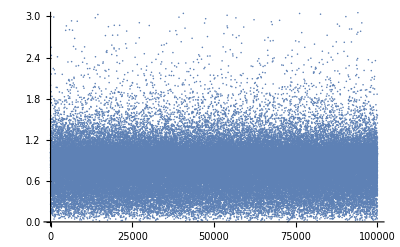

```mathematica
ListPlot[Table[{i,Min[phystest2[[i]]]},{i,10^5}],PlotRange->{0,3}]
(*Points that are less than 1 are entangled and greater than one are seperable*)
```

```mathematica
SympEig={};
Do[AppendTo[SympEig,Min[Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]]]//Chop]];,{i,10^5}];
```

```mathematica
Dynamic[i]
```

```mathematica
SympEig[[1]]
```

0.504792

```mathematica
Table[{i,{SympEig[[i]]}},{i,10^5}];
```

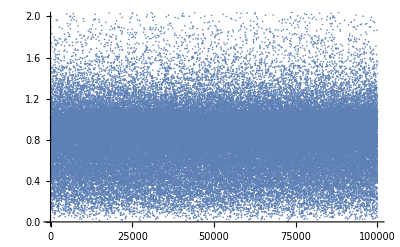

```mathematica
ListPlot[Table[{i,SympEig[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Negativity={};
Do[AppendTo[Negativity,(1-SympEig[[i]])/(2SympEig[[i]])];,{i,10^5}];
Negativity[[1]]
```

1.4337

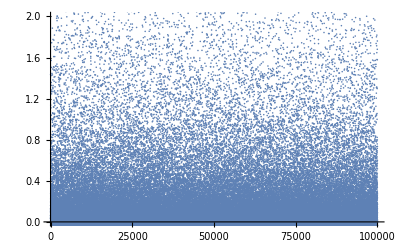

```mathematica
Table[{i,{Negativity[[i]]}},{i,10^5}];
ListPlot[Table[{i,Negativity[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
LogNeg={};
Do[AppendTo[LogNeg,-Log[SympEig[[i]]]];,{i,10^5}];
LogNeg[[1]]
```

1.35258

```mathematica
Dynamic[i]
```

```mathematica
Table[{i,{LogNeg[[i]]}},{i,10^5}];
```

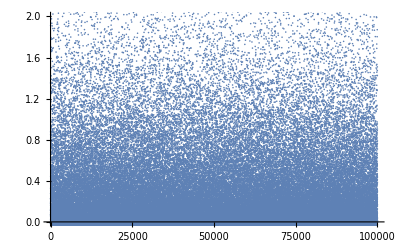

```mathematica
ListPlot[Table[{i,LogNeg[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Subscript[Determinantσ, P.T]={};
```

```mathematica
Do[AppendTo[Subscript[Determinantσ, P.T],(a[[i]]b[[i]]-cp[[i]]^2)(a[[i]]b[[i]]-cm[[i]]^2)];,{i,10^5}];
Subscript[Determinantσ, P.T][[1]]
```

951.141

```mathematica
Table[{i,{Determinantσ[[i]]}},{i,10^5}];
```

```mathematica
Purity={};
```

```mathematica
Do[AppendTo[Purity,1/(√(Subscript[Determinantσ, P.T][[i]]))];,{i,10^5}];
```

```mathematica
Purity[[1]]
```

0.0108912

```mathematica
Table[{i,{Purity[[i]]}},{i,10^5}];
```

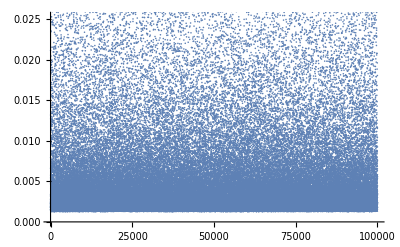

```mathematica
ListPlot[Table[{i,Purity[[i]]},{i,10^5}]]
```

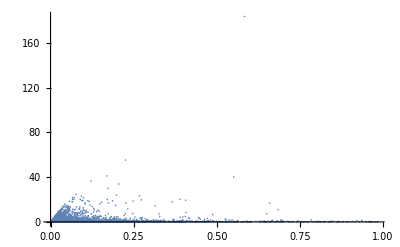

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,Negativity[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 40, now is nearly 200*)
```

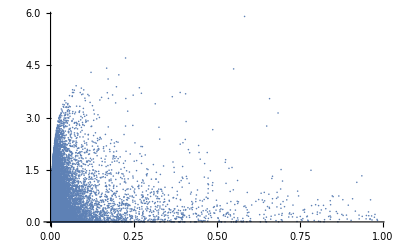

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,LogNeg[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 4, now is around 6*)
```